# Neural network research with the Wolfram Language

## Ian Wright, GitHub

## #WolframTechConf

## ABSTRACT

Wolfram Language provides an advanced framework for rapidly prototyping neural network applications and exploring research ideas. In this talk, I demonstrate the language features that helped me develop a novel neural network that learns compact non-differentiable Boolean functions.

## Utilities

```mathematica
BPlot[f_,y_]:=Plot[f[x,y],{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->{"x","output"}]
ActivationPlot[f_,contours_:10]:=ContourPlot[f[x,y],{x,0,1},{y,0,1},FrameLabel->{x,w},PlotLegends->BarLegend[{Automatic,{0,1}}],PlotRange->All,ColorFunction->(If[#>1/2,Lighter[Red,#],Lighter[Darker[Gray,0.5],#]]&),ColorFunctionScaling->False,GridLines->{{1/2},{1/2}},GridLinesStyle->Black,Contours->Range[0,1,1/contours]]
MarginPacking[]:=Manipulate[
Block[{m,eps,thresholdLine,marginLine,representativeLine,augmentation},
m=Min[x,w];
eps=0.01;
augmentation=Mean[{x,w}]Abs[m-1/2];
thresholdLine=Line[{{1/2,-1},{1/2,1}}];
marginLine={Line[{{m,0.2},{1/2,0.2}}],Text[Style["margin",Bold,FontFamily->"Helvetica"],{m+(1/2-m)/2,0.3}]};
representativeLine={Line[{{m,-0.8},{m,1}}],Text[Style["representative bit",Bold,FontFamily->"Helvetica"],{m,-0.9}]};
Labeled[Plot[
{
Callout[If[m<=1/2,
If[x>=(m+augmentation-eps)&&x<=(m+augmentation+eps),1,Nothing],
If[x>=(1/2+augmentation-eps)&&x<=(1/2+augmentation+eps),1,Nothing]
],Style["augmented bit",Bold,FontColor->Gray],{If[m>1/2,1/2+augmentation,m+augmentation],1.2},CalloutStyle->{Gray},Background->Transparent],
If[m<=1/2,
If[x>m && x<=(m+augmentation),1,Nothing],
If[x>1/2&&x<(1/2+augmentation),1,Nothing]
]
},
{x,0,1},
PlotRange->{{If[m>1/2,0.45,0],If[m>1/2,1,0.55]},{-1,1}},
PlotStyle->Transparent,
Filling->{1->1,2->-0.8},
FillingStyle->LightGray,
Axes->{True,False},
Ticks->{True,False},
Epilog->{Directive[Black],representativeLine,Directive[Gray,Dashed],thresholdLine,marginLine},
ImagePadding->{{0,0},{0,30}},
AspectRatio->2/3
],If[m>1/2,Style["high margin",FontFamily->"Helvetica"],Style["low margin",FontFamily->"Helvetica"]],Bottom]
],{x,0,1},{w,0,1}
]
MarginPack[representativeBit_,x_List]:=Module[{μ=Mean[x],δ},
δ=μ Abs[(representativeBit-1/2)];
If[representativeBit>1/2,Evaluate[1/2+δ],Evaluate[representativeBit+δ]]
]
```

## R&D goals

Neural nets are differentiable for backpropagation

Can’t learn discrete functions (e.g. boolean functions)

Nets can be huge (e.g. 16 or 32-bits per weight)

Query-time can be expensive (floating point operations)

Idea: ∂𝔹-nets

-Graphics-

### Hard and soft bits

```mathematica
Hard[x_]:=If[x>1/2,True,False]
Hard[x_List]:=Hard/@x
```

```mathematica
Hard[{0.2,0.6,0.45}]
```

{False,True,False}

### Hard equivalence

Hard(SoftNet(x)) = HardNet(Hard(x))

## Learning to mask

We need a differentiable version of the boolean function:

```mathematica
And[x,w]
```

x&&w

```mathematica
ResourceFunction["TruthTable"][And[x,w],{x,w}]
```

x | w | x&&w
True | True | True
True | False | False
False | True | False
False | False | False

### Product logic

```mathematica
ProductAnd[x_Real,w_Real]:=x w
```

```mathematica
Manipulate[BPlot[ProductAnd,w],{{w,1},0,1}]
```

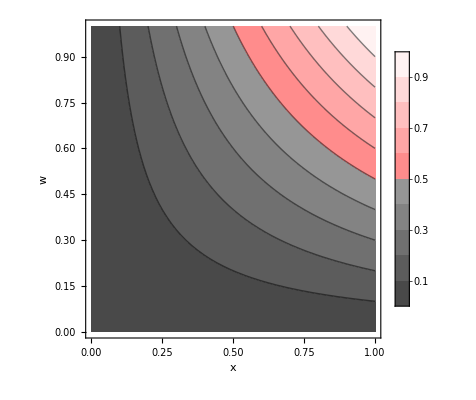

```mathematica
ActivationPlot[ProductAnd]
```

Product logic is

gradient rich

but not hard equivalent

### Gödel logic

```mathematica
GodelAnd[x_Real,w_Real]:=Min[x,w]
```

```mathematica
Manipulate[BPlot[GodelAnd,w],{{w,1},0,1}]
```

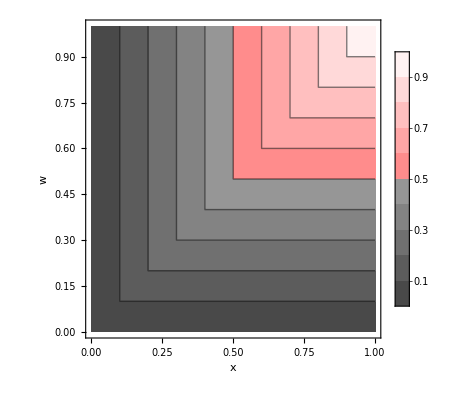

```mathematica
ActivationPlot[GodelAnd]
```

Godel logic is

hard equivalent

but not gradient rich

### Margin packing

Idea: pack the hard-equivalent margin with gradient-rich information

```mathematica
MarginPacking[]
```

```mathematica
DAnd[x_,w_]:=MarginPack[Min[x,w],{x,w}]
```

```mathematica
DAnd[x,w]//PiecewiseExpand
```

Piecewise[{{1/4 (5 w-2 w^2+x-2 w x), w<1/2&&w-x≤0}, {1/4 (2-w+2 w^2-x+2 w x), w>1/2&&x>1/2&&w-x≤0}, {1/4 (3 w+2 w^2-x+2 w x), (w==1/2&&w-x≤0)||(w≥1/2&&w-x≤0&&x≤1/2)}, {1/4 (w+5 x-2 w x-2 x^2), x<1/2&&w-x>0}, {1/4 (2-w-x+2 w x+2 x^2), w>1/2&&x>1/2&&w-x>0}, {1/4 (-w+3 x+2 w x+2 x^2), True}}]

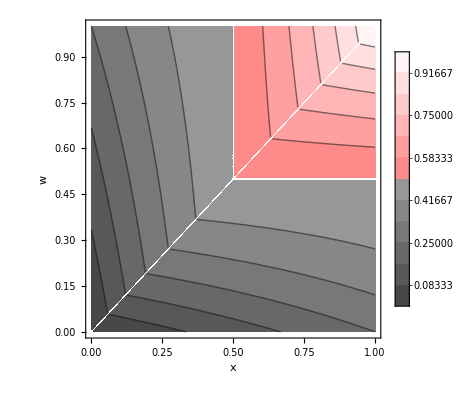

```mathematica
ActivationPlot[DAnd,12]
```

∂𝔹 logic is

hard equivalent

and gradient rich

## Neural network layers

```mathematica
Get["neural-logic.m",Path->SetDirectory["/home/wright/mywork/db-nets/prototype"]]
```

### Boolean majority

```mathematica
Majority[True,True,False]
```

True

```mathematica
Majority[False, False,True]
```

False

```mathematica
BooleanConvert[Majority[x1,x2,x3,x4,x5,x6],"DNF"]
```

(x1&&x2&&x3&&x4)||(x1&&x2&&x3&&x5)||(x1&&x2&&x3&&x6)||(x1&&x2&&x4&&x5)||(x1&&x2&&x4&&x6)||(x1&&x2&&x5&&x6)||(x1&&x3&&x4&&x5)||(x1&&x3&&x4&&x6)||(x1&&x3&&x5&&x6)||(x1&&x4&&x5&&x6)||(x2&&x3&&x4&&x5)||(x2&&x3&&x4&&x6)||(x2&&x3&&x5&&x6)||(x2&&x4&&x5&&x6)||(x3&&x4&&x5&&x6)

If we sort(x) the input bits then the ‘middle’ soft-bit is representative and therefore hard-equivalent to Boolean majority.

```mathematica
NetChain[{
   FunctionLayer[ReverseSort /@ # &],
   PartLayer[{All, Ceiling[(inputSize + 1) / 2]}]
}]
```

```mathematica
{softNet,hardNet}=HardNeuralMajority[8];
```

#### The soft net

```mathematica
softNet
```

NetGraph[…]

```mathematica
softInput={{0.52,0.8,0.3,0.7,0.2,0.7,0.1,0.99}};
```

```mathematica
softOutput=softNet[softInput]
```

{0.52}

#### The hard net

```mathematica
hardNet
```

Function[{neurallogic`Private`inputsAndWeights},Block[{neurallogic`Private`inputs,neurallogic`Private`weights},{neurallogic`Private`inputs,neurallogic`Private`weights}=neurallogic`Private`inputsAndWeights;{(Block[{neurallogic`Private`input=#1},ConfirmAssert[ListQ[neurallogic`Private`input],Null,HardMajority semantics check];Majority@@neurallogic`Private`input]&)/@neurallogic`Private`inputs,neurallogic`Private`weights}]]

```mathematica
hardOutput=First[hardNet[{Harden[softInput],{}}]]
```

{True}

#### Hard equivalence

```mathematica
Harden[softOutput]==hardOutput
```

True

## A classification problem

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
Length[data]
```

1728

### Feature encoding

#### Utilities

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
InputEncoders[encoders_]:=Drop[encoders,-1]
OutputEncoder[encoders_]:=Last[encoders]
InputEncoder[inputEncoders_]:=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Normal[inputEncoders]],Sequence@@Normal[Normal[inputEncoders]]
];
Net[inputSize_,classes_,inputEncoder_,outputEncoder_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,64],
HardNeuralNOT[64,Length[classes]]
}];
trainableNet=NetGraph[
<|"Input"->inputEncoder,"Net"->softNet,"Loss"->HardClassificationLoss[]|>,
{"Input"->"Net"->"Loss",NetPort["Acceptability"]->NetPort["Loss","Target"]},
"Acceptability"->outputEncoder
];
{trainableNet,hardNet}
]
TrainNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
GetTrainedNet[result_]:=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{}
]
EvaluateNet[hardNetFunction_,testData_,inputEncoder_,outputEncoder_]:=Module[{predictions,eval},
predictions=HardNetClassify[hardNetFunction,testData,NetDecoder[outputEncoder],inputEncoder&,#["Acceptability"]&];eval=HardNetClassifyEvaluation[predictions];
{predictions,eval}
]
GetNetWeights[trainedNeuralLogicNet_]:=Flatten[ExtractWeights[trainedNeuralLogicNet]]
```

#### Input encoder

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

```mathematica
encoders=Encoders[trainData]
```

<|PurchasePrice→NetEncoder[…],MaintenanceCost→NetEncoder[…],Doors→NetEncoder[…],Passengers→NetEncoder[…],Cargo→NetEncoder[…],Safety→NetEncoder[…],Acceptability→NetEncoder[…]|>

```mathematica
inputEncoder=InputEncoder[InputEncoders[encoders]]
```

NetGraph[…]

### Define ∂𝔹-net

```mathematica
inputSize=Total[First[#["Output"]]&/@Normal/@Values[InputEncoders[encoders]]]
```

21

```mathematica
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]]
```

{unacceptable,acceptable,very good,good}

```mathematica
{softNet,hardNet}=Net[inputSize,classes,inputEncoder,OutputEncoder[encoders]];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[…]

### Train ∂𝔹-net

```mathematica
result=TrainNet[softNet,trainData,testData]
```

NetTrain::badtrgdevgpu: TargetDevice -> GPU could not be used. Please ensure that you have a compatible NVIDIA graphics card and have installed the latest drivers from http://www.nvidia.com/Download/index.aspx.

$Failed

```mathematica
trainedNet=GetTrainedNet[result]
```

NetGraph[…]

### Evaluate ∂𝔹-net

```mathematica
{softNetClassifier,hardNetClassifier}=NetGraph[
<|"TrainedNet"->#|>,{},"Output"->NetDecoder[outputEncoder]
]&/@{trainedNet,HardenNet[trainedNet]};
```

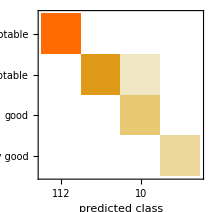
{Classifier Measurements
Classifier method | Net
Number of test examples | 173
Accuracy | (99.40.6) %
Accuracy baseline | (65.4.) %
Geometric mean of probabilities | 0.981 ± 0.0053
Mean cross entropy | 0.0196 ± 0.0054
Single evaluation time | 4.85 ms/example
Batch evaluation speed | 2.48 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 173
Accuracy | (99.40.6) %
Accuracy baseline | (65.4.) %
Geometric mean of probabilities | 0.981 ± 0.0053
Mean cross entropy | 0.0196 ± 0.0054
Single evaluation time | 2.84 ms/example
Batch evaluation speed | 3.24 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{softNetClassifier,hardNetClassifier}
```

### Bind weights with hard net

```mathematica
booleanClassifier=HardNetFunction[hardNet,trainedNet]
```

```mathematica
HardNetBooleanExpression[booleanClassifier,inputSize]//Dimensions
```

{4,64}

```mathematica
HardNetBooleanExpression[booleanClassifier,inputSize][[1]]
```

{!(b2||b13),!(b3||b4||b6||b7||b21),b4||b6||b15||b19,b7||b15||b18||b19||b21,!(b13||b18),b2||b3||b7||b8||b15||b19,b3||b4||b6||b15||b18||b19,b7||b12||b13||b15||b17||b19,b3||b4||b7||b18,!(b9||b10||b13||b17||b18||b20),b7||b15||b19,b4||b6||b11||b15||b18||b19||b20,b3||b4||b7||b9||b10||b15||b17||b19,!(b1||b5),b3||b4||b7||b15||b16||b18||b21,b3||b10||b12||b13||b15||b16||b19,!(b3||b4||b6||b7||b21),!(b1||b8),!(b2||b6||b10||b17||b20),!(b9||b10||b13||b17||b18),!(b2||b14),!(b1||b4||b5||b7),b6||b7||b15||b19,!(b1||b5||b10||b13||b14),b3||b4||b6||b15||b19,b1||b2||b7||b11||b15||b18||b19,b15||b18||b19||b20,b3||b4||b7||b15||b17||b19||b20,!(b1||b8||b17||b20),b4||b6||b7||b11||b15||b19,!(b13||b14),b7||b11||b15||b19,b1||b6||b7||b15||b19,!(b3||b4||b7||b11||b18||b21),b3||b4||b6||b7||b11||b18||b19||b20,!(b9||b10||b17||b20),!(b1||b17||b20),b3||b5||b15||b18||b19,b1||b3||b5||b7||b8||b15||b19||b21,b3||b4||b11||b15||b19||b21,b3||b7||b15||b18||b19,b3||b4||b7||b14||b15||b18||b19||b21,!(b9||b10||b12||b14||b17),!(b2||b3||b6),b3||b4||b9||b10||b13||b15||b17||b19||b21,!(b3||b4||b6||b7||b9||b17||b21),b11||b14||b15||b17||b19||b20,b3||b4||b11||b15||b19,!(b2||b6||b16||b17||b20),!(b9||b10||b12||b14||b16||b17),b3||b8||b15||b19,!(b1||b4||b5||b20),b11||b15||b16||b17||b19||b21,b3||b7||b15||b19,!(b8||b20),b3||b4||b6||b7||b15||b19,!(b1||b2||b5||b8),b3||b9||b10||b13||b15||b17||b19||b21,b3||b4||b5||b8||b15||b18||b19,!(b5||b8||b17),!(b3||b4||b7||b21),b1||b3||b8||b15||b18||b19,b4||b6||b15||b19,b1||b3||b7||b8||b15||b19}

### Evaluate boolean classifier

```mathematica
{predictions,summary}=EvaluateNet[booleanClassifier,testData,InputEncoder,OutputEncoder];
```

```mathematica
summary["Accuracy"]
```

0.99422

#### Size of boolean classifier

```mathematica
weights=GetNetWeights[result["TrainedNet"]];
```

```mathematica
booleanWeightSize=Quantity[Length[weights]/8/1024//N,"Kilobytes"]
```

0.195313 kB

The size of a (minimal) MLP for this problem is ~16 kB

∂𝔹-net is ~80 times smaller for identical accuracy

## Conclusion

### Wolfram Language for Machine Learning research

Rapid prototyping of new ideas

Neural network functions: high level and unified

Yet configurable

Arbitrary code into your network. E.g. FunctionLayer

Different forward and backward passes. E.g. CompiledFunction

### More on ∂𝔹-nets

Lossless hardening with ∂𝔹 nets. I. Wright. In "Differentiable Almost Everything: Differentiable Relaxations, Algorithms, Operators, and Simulators", ICML 2023 Workshop, Honolulu, 2023.

GitHub repo: https://github.com/Z80coder/db-nets

### Acknowledgements

Thanks to GitHub Next for sponsoring this research